Updating from Wolfram Research server ...

Updating from Wolfram Research server ...

ItemAspectRatio::shdw: Symbol ItemAspectRatio appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

~/Desktop/piapprox.gif

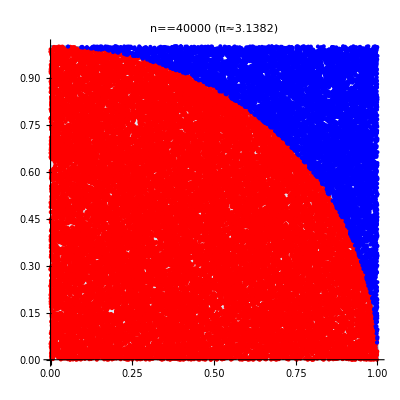

```mathematica
tinyColor[color_,point_]:={PointSize[Small],color,Point[point]}
colorChoose[point_]:=If[Norm[point]≤1,tinyColor[Red,point],tinyColor[Blue,point]]

darts=RandomReal[{0,1},{40000,2}];
coloredDarts=ParallelMap[colorChoose,darts];
insides=Map[Boole[Norm[#]≤1]&,darts];
piapprox=Accumulate[insides]/Range[Length[darts]];

(*This export command generates an animated gif,preserving the order the points are created in,but is exceedingly slow.A better method for generating a static image is given below*)
Export["~/Desktop/piapprox.gif",Table[Show[Plot[Sqrt[1-x^2],{x,0,1},Filling->Axis,AspectRatio->1,PlotLabel->n==max TildeTilde[π,4.0*piapprox[[max]]]],Graphics[coloredDarts[[1;;max]]],ImageSize->{500,500}],{max,3000,Length[darts],Length[darts]/10}],"DisplayDurations"->ConstantArray[1,9]~Join~{3}]

(*Plotting a large number of Graphics[] objects is very slow relative to using ListPlot for points.Splitting the list of random points into inner and outer lists destroys the order in which the points are created (so it cannot be used for animations) but is much faster for static images.*)
inner=Select[darts,Norm[#]≤1&];
outer=Select[darts,Norm[#]>1&];
Show[Plot[Sqrt[1-x^2],{x,0,1},Filling->Axis,AspectRatio->1,PlotLabel->n==Length[darts] TildeTilde[π,4.0*piapprox[[-1]]]],ListPlot[{inner,outer},PlotStyle->{{PointSize[Tiny],Red},{PointSize[Tiny],Blue}},ImageSize->{500,500}]]
```